```mathematica
Manipulate[
prbls1=ContourPlot[
{x^2==u y,y^2==v x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
point=Graphics[
{PointSize[Large],
Point[
{Root[-u^2 v+#1^3&,1],
Root[-u v^2+#1^3&,1]}
]}];
Show[prbls1,point],
{u,-1,1},{v,-1,1}
]
```

```mathematica
(*step=0.05;
v=1;
plots1=Table[
parabolas=ContourPlot[
{x^2==u y,y^2==v x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
point=Graphics[
{PointSize[Large],
Point[
{Root[-u^2 v+#1^3&,1],
Root[-u v^2+#1^3&,1]}
]}];
Show[parabolas,point],
{u,1,-1,-step}
];
u=-1;
plots2=Table[
parabolas=ContourPlot[
{x^2==u y,y^2==v x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
point=Graphics[
{PointSize[Large],
Point[
{Root[-u^2 v+#1^3&,1],
Root[-u v^2+#1^3&,1]}
]}];
Show[parabolas,point],
{v,1,-1,-step}
];
v=-1;
plots3=Table[
parabolas=ContourPlot[
{x^2==u y,y^2==v x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
point=Graphics[
{PointSize[Large],
Point[
{Root[-u^2 v+#1^3&,1],
Root[-u v^2+#1^3&,1]}
]}];
Show[parabolas,point],
{u,-1,1,step}
];
u=1;
plots4=Table[
parabolas=ContourPlot[
{x^2==u y,y^2==v x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
point=Graphics[
{PointSize[Large],
Point[
{Root[-u^2 v+#1^3&,1],
Root[-u v^2+#1^3&,1]}
]}];
Show[parabolas,point],
{v,-1,1,step}
];
plots=Join[plots1,plots2,plots3,plots4];
Export["parabolaContour.gif",plots];
*)
```

```mathematica
Manipulate[
prbls2=ContourPlot[
{x^2==u[t] y,y^2==v[t] x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
aux=Graphics[
{PointSize[Large],Point[{Cos[t],Sin[t]}],
Dashed,Red,Circle[]
}];
Show[prbls2,aux],
{t,0,2Pi},
Initialization:>(u[t_]:=Cot[t]Cos[t];v[t_]:=Tan[t]Sin[t])
]
```

```mathematica
(*u[t_]:=Cot[t]Cos[t];v[t_]:=Tan[t]Sin[t];
plots=Table[
parabolas=ContourPlot[
{x^2==u[t] y,y^2==v[t] x},
{x,-1,1},{y,-1,1},
Frame->False,Axes->True,
MaxRecursion->5];
aux=Graphics[
{PointSize[Large],Point[{Cos[t],Sin[t]}],
Dashed,Red,Circle[]
}];
Show[parabolas,aux],
{t,0,2Pi,0.05}
];
Export["parabolaCircle.gif",plots];*)
```

```mathematica
p=0.5;q=1.5;r=0.4;s=1.8;
```

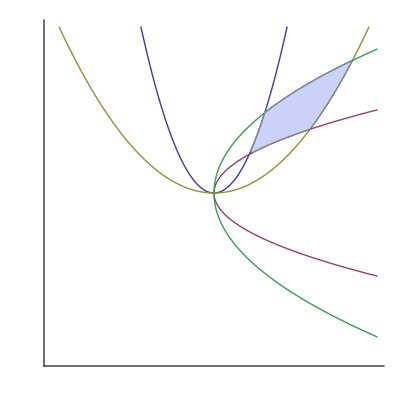

```mathematica
parabolas=ContourPlot[
{x^2== r y,y^2== p x,
x^2== s y,y^2== q x},
{x,-2,2},{y,-2,2},
Frame->False,Axes->True,Ticks->False,
MaxRecursion->5];
region1=RegionPlot[x^2≥r y&&y^2≤ q x&&y^2≥p x&&x^2≤s y,
{x,-2,2},{y,-2,2},MaxRecursion->5];
Show[parabolas,region1]
```

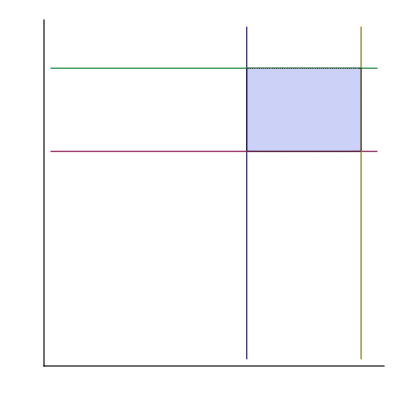

```mathematica
lines=ContourPlot[
{x==r,y==p,x==s,y==q},
{x,-2,2},{y,-2,2},
Frame->False,Axes->True,Ticks->False,
MaxRecursion->5];
region2=RegionPlot[x≥r&&x≤s&&y≥p&&y≤q,
{x,-2,2},{y,-2,2},MaxRecursion->5];
Show[lines,region2]
```